```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/berni/Dropbox/Projects/RapidiX/RapidiX

## NNLO Expansion Tests

```mathematica
RapidityNNLOgg[[;;,2]]//Total
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

0

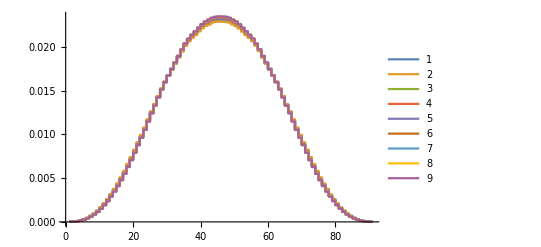

```mathematica
Table[Get["Results/NNLODistributions_zb"<>ToString[i]<>".txt"];
fac[i]RapidityNNLOgg[[;;,2]]/Total[RapidityNNLOgg[[;;,2]]],{i,0,8}]/.fac[0]->1/._fac->1;
ListStepPlot[%,PlotLegends->Automatic]
```

```mathematica
last=RapidityNNLOgg[[;;,2]]/Total[RapidityNNLOgg[[;;,2]]];
```

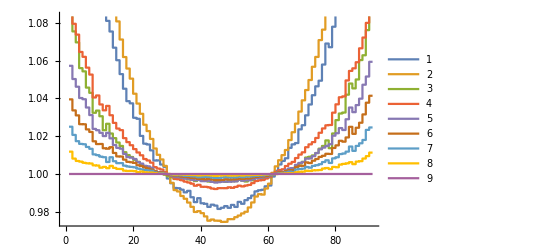

```mathematica
Table[Get["Results/NNLODistributions_zb"<>ToString[i]<>".txt"];
RapidityNNLOgg[[;;,2]]/Total[RapidityNNLOgg[[;;,2]]]/last,{i,0,8}];
ListStepPlot[%,PlotLegends->Automatic]
```

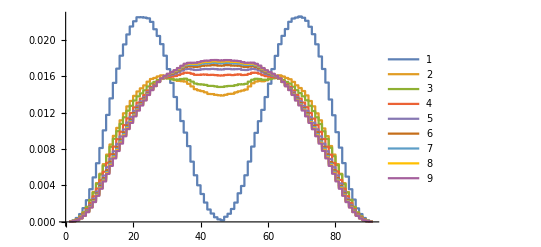

```mathematica
Table[Get["Results/NNLODistributions_zb"<>ToString[i]<>".txt"];
fac[i](RapidityNNLOqg[[;;,2]]+RapidityNNLOgq[[;;,2]])/Total[RapidityNNLOqg[[;;,2]]+RapidityNNLOgq[[;;,2]]],{i,0,8}]/.fac[0]->1/._fac->1;
ListStepPlot[%,PlotLegends->Automatic]
```

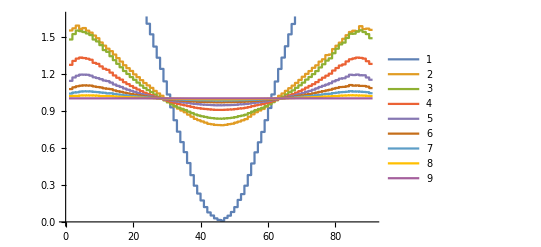

```mathematica
last=(RapidityNNLOqg[[;;,2]]+RapidityNNLOgq[[;;,2]])/Total[RapidityNNLOqg[[;;,2]]+RapidityNNLOgq[[;;,2]]];
Table[Get["Results/NNLODistributions_zb"<>ToString[i]<>".txt"];
fac[i](RapidityNNLOqg[[;;,2]]+RapidityNNLOgq[[;;,2]])/Total[RapidityNNLOqg[[;;,2]]+RapidityNNLOgq[[;;,2]]]/last,{i,0,8}]/.fac[0]->1/._fac->1;
ListStepPlot[%,PlotLegends->Automatic]
```

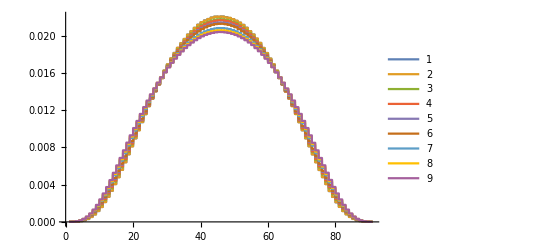

```mathematica
Table[Get["Results/NNLODistributions_zb"<>ToString[i]<>".txt"];
fac[i]RapidityNNLOqqbar[[;;,2]]/Total[RapidityNNLOqqbar[[;;,2]]],{i,0,8}]/.fac[0]->1/._fac->1;
ListStepPlot[%,PlotLegends->Automatic]
```

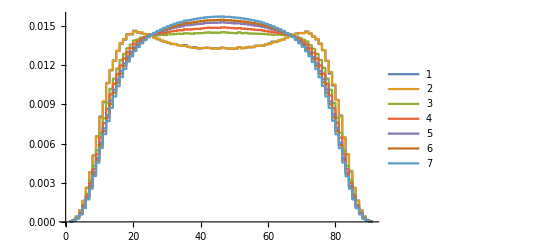

```mathematica
Table[Get["Results/NNLODistributions_zb"<>ToString[i]<>".txt"];
fac[i]RapidityNNLOqq[[;;,2]]/Total[RapidityNNLOqq[[;;,2]]],{i,2,8}]/.fac[0]->1/._fac->1;
ListStepPlot[%,PlotLegends->Automatic]
```

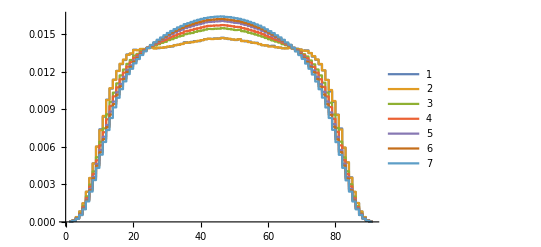

```mathematica
Table[Get["Results/NNLODistributions_zb"<>ToString[i]<>".txt"];
RapidityNNLOqQ2[[;;,2]]/Total[RapidityNNLOqQ2[[;;,2]]],{i,2,8}]/._fac->1;
ListStepPlot[%,PlotLegends->Automatic]
```

## NNLO Expansion Tests with exact as a complement

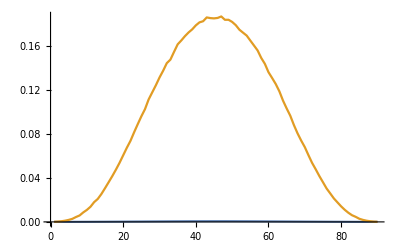

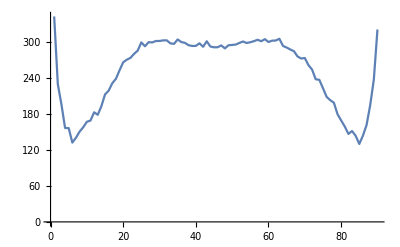

```mathematica
Get["Results/NNLOExact1.txt"]
exact=RapidityNNLOqQ2[[;;,2]];
Get["Results/NumericalNNLO.txt"]
numerical=RapidityNNLOgg[[;;,2]];
ListLinePlot[{exact,numerical}]
ListLinePlot[numerical/exact]
```

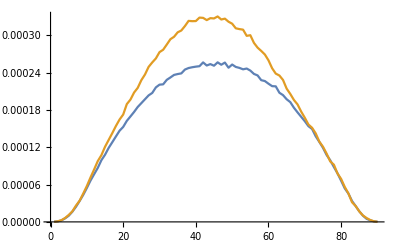

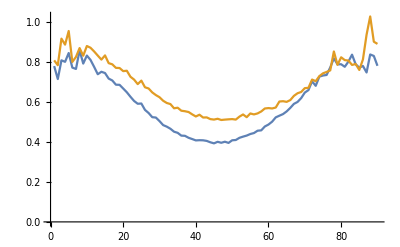

```mathematica
Get["Results/NNLOExact2.txt"]
exact2=RapidityNNLOqQ2[[;;,2]];
Get["Results/NNLOExact3.txt"]
exact3=RapidityNNLOqQ2[[;;,2]];
ListLinePlot[{exact2,exact3}]
ListLinePlot[{exact2/exact,exact3/exact}]
```

{0.00224539,0.00521604,0.00772705,0.00948283,0.0106268,0.0113691,0.0119371}

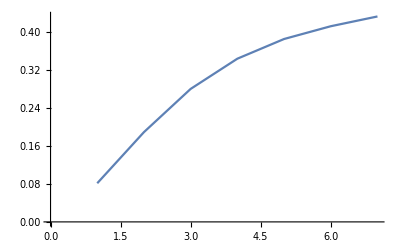

```mathematica
Table[Get["Results/NNLODistributions_zb"<>ToString[i]<>".txt"];
Total[RapidityNNLOqQ2[[;;,2]]],{i,2,8}]/.fac[0]->1/._fac->1
ListLinePlot[%/Total[exact]]
```

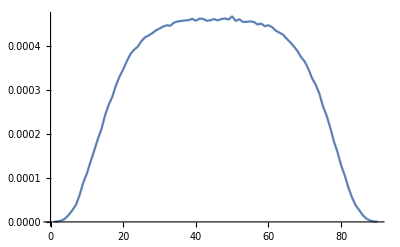

```mathematica
Get["Results/InclusiveNNLOqQ2.txt"];
IncRap=RapidityNNLOqQ2[[;;,2]];
ListLinePlot[IncRap]
```

{200.23,199.191,199.993,199.975,199.904,199.919,199.977}

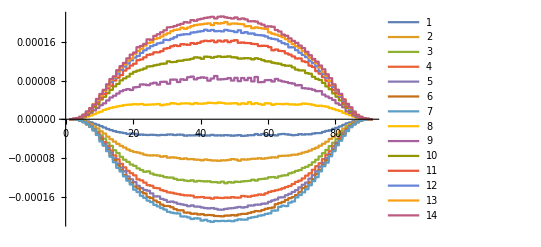

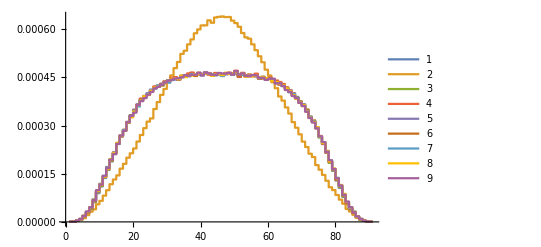

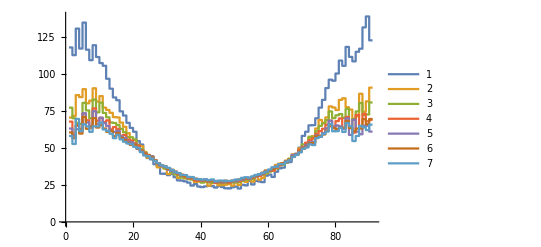

```mathematica
data=Table[Get["Results/NNLODistributions_Matched_zb"<>ToString[i]<>".txt"];
RapidityNNLOqQ2[[;;,2]],{i,2,8}]/._fac->1;
data2=Table[Get["Results/NNLODistributions_zb"<>ToString[i]<>".txt"];
RapidityNNLOqQ2[[;;,2]],{i,2,8}]/._fac->1;
Abs[(Total/@(data-data2))/(Total/@data2)] 100
ListStepPlot[Join[data,data2],PlotLegends->Automatic,PlotRange->All]
ListStepPlot[Join[{IncRap,exact},IncRap+#&/@(data+data2)],PlotLegends->Automatic,PlotRange->All]
ListStepPlot[#/exact/Total[#]&/@data2,PlotLegends->Automatic,PlotRange->All]
```

```mathematica
Total[last]
```

7.83301

```mathematica
RapidityNNLOgg[[;;,2]]//Total
```

10.9369

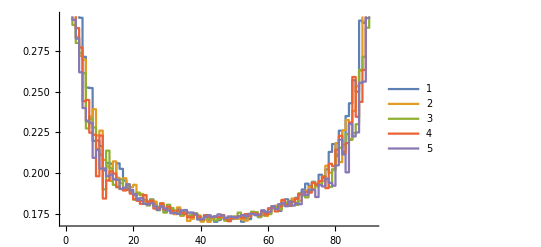

```mathematica
data=Table[Get["Results/NNLODistributions_Subtracted_zb"<>ToString[i]<>".txt"];
(RapidityNNLO[[;;,2]]),{i,4,8}]/._fac->1;
Get["Results/NumericalNNLO.txt"]
last=RapidityNNLO[[;;,2]];
ListStepPlot[#/last&/@data,PlotLegends->Automatic]
```

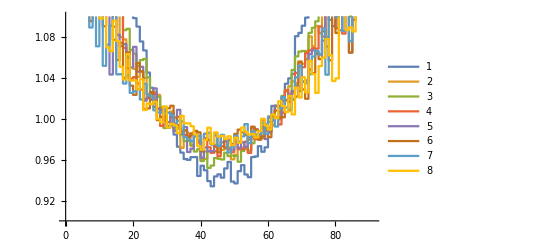

```mathematica
data=Table[Get["Results/NNLODistributions_Subtracted_zb"<>ToString[i]<>".txt"];
(RapidityNNLOgg[[;;,2]]),{i,1,8}]/._fac->1;
Get["Results/NumericalNNLO.txt"]
last=RapidityNNLOgg[[;;,2]];
ListStepPlot[#/last&/@data,PlotLegends->Automatic,PlotRange->{0.9,1.1}]
```

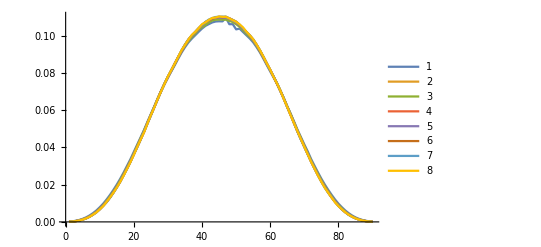

```mathematica
data=Table[Get["Results/NNLODistributions_Subtracted_zb"<>ToString[i]<>"_625.txt"];
(RapidityNNLOgg[[;;,2]]),{i,1,8}]/._fac->1;
ListLinePlot[data,PlotLegends->Automatic,PlotRange->All]
```

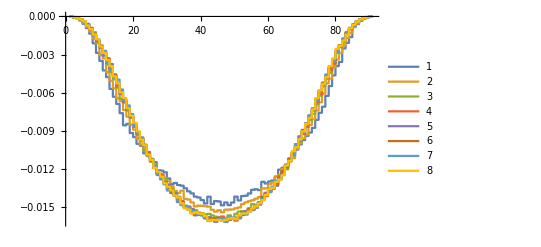

```mathematica
data=Table[Get["Results/NNLODistributions_Subtracted_zb"<>ToString[i]<>".txt"];
(RapidityNNLOqg[[;;,2]]+RapidityNNLOgq[[;;,2]]),{i,1,8}]/._fac->1;
ListStepPlot[data,PlotLegends->Automatic,PlotRange->All]
```

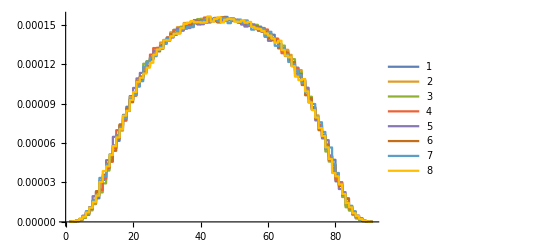

```mathematica
data=Table[Get["Results/NNLODistributions_Subtracted_zb"<>ToString[i]<>".txt"];
RapidityNNLOqqbar[[;;,2]],{i,1,8}]/._fac->1;
ListStepPlot[data,PlotLegends->Automatic,PlotRange->All]
```

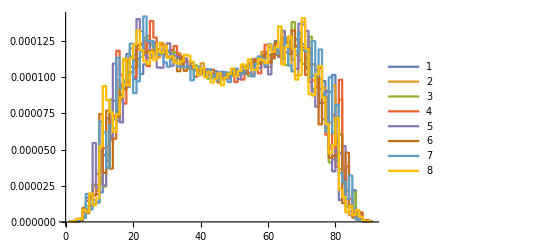

```mathematica
data=Table[Get["Results/NNLODistributions_Subtracted_zb"<>ToString[i]<>".txt"];
RapidityNNLOqq[[;;,2]],{i,1,8}]/._fac->1;
ListStepPlot[data,PlotLegends->Automatic,PlotRange->All]
```

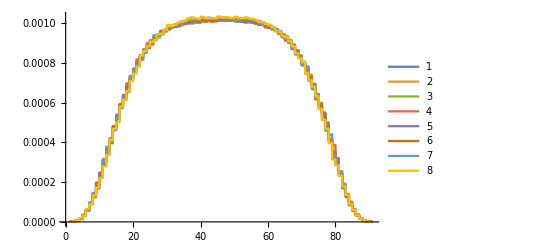

```mathematica
data=Table[Get["Results/NNLODistributions_Subtracted_zb"<>ToString[i]<>"_625.txt"];
RapidityNNLOqQ2[[;;,2]],{i,1,8}]/._fac->1;
ListStepPlot[data,PlotLegends->Automatic,PlotRange->All]
```

## NNLO Distribution

```mathematica
dists=Table[Get["Results/Rapidity/Distributions_"<>StringReplace[ToString[N[i/10]]<>"_125.txt",{"._"->"_"}]];
{i/10//N,Total[RapidityNNLO[[;;,2]]]},{i,0,44}];
```

```mathematica
dists
```

{{0.,9.68177},{0.1,9.67634},{0.2,9.6439},{0.3,9.56922},{0.4,9.471},{0.5,9.35696},{0.6,9.20091},{0.7,9.0193},{0.8,8.82759},{0.9,8.63128},{1.,8.39879},{1.1,8.12811},{1.2,7.81866},{1.3,7.49896},{1.4,7.17656},{1.5,6.84694},{1.6,6.50772},{1.7,6.15035},{1.8,5.77513},{1.9,5.38026},{2.,4.99851},{2.1,4.61609},{2.2,4.21798},{2.3,3.83592},{2.4,3.47121},{2.5,3.11877},{2.6,2.76819},{2.7,2.44039},{2.8,2.12741},{2.9,1.83436},{3.,1.5608},{3.1,1.31049},{3.2,1.08544},{3.3,0.882383},{3.4,0.70238},{3.5,0.546452},{3.6,0.413683},{3.7,0.303867},{3.8,0.21527},{3.9,0.146369},{4.,0.0941393},{4.1,0.056432},{4.2,0.030721},{4.3,0.014362},{4.4,0.0051556}}

```mathematica
Get["XS/Inclusive/InclusiveXS/XS_zb.txt"][[4,5]]/.zb->1-0.642921136448946
```

105.855+1.55228×10^-23 ALARM-118.795 Log[MH2/muf2]+39.5595 Log[MH2/muf2]^2-4.04342 Log[MH2/muf2]^3

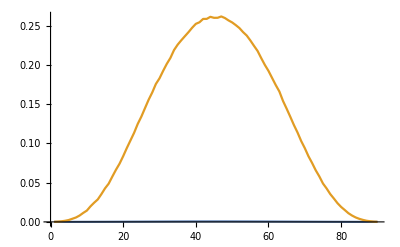

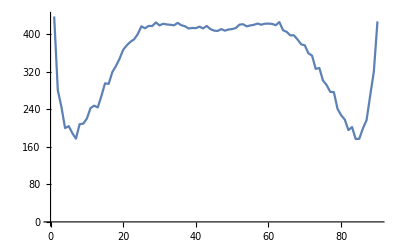

```mathematica
Get["Results/NNLOExact1.txt"]
exact=RapidityNNLOqQ2[[;;,2]];
Get["Results/NumericalNNLO.txt"]
numerical=RapidityNNLOgg[[;;,2]];
ListLinePlot[{exact,numerical}]
ListLinePlot[numerical/exact]
```

```mathematica
Get["Results/NNLOExact2.txt"]
exact2=RapidityNNLOqQ2[[;;,2]];
Get["Results/NNLOExact3.txt"]
exact3=RapidityNNLOqQ2[[;;,2]];
ListLinePlot[{exact2,exact3}]
ListLinePlot[{exact2/exact,exact3/exact}]
```

-Graphics-

-Graphics-

```mathematica
Table[Get["Results/NNLODistributions_zb"<>ToString[i]<>".txt"];
Total[RapidityNNLOqQ2[[;;,2]]],{i,2,8}]/.fac[0]->1/._fac->1
ListLinePlot[%/Total[exact]]
```

{0.00224539,0.00521604,0.00772705,0.00948283,0.0106268,0.0113691,0.0119371}

-Graphics-

```mathematica
Get["Results/InclusiveNNLOqQ2.txt"];
IncRap=RapidityNNLOqQ2[[;;,2]];
ListLinePlot[IncRap]
```

-Graphics-

```mathematica
data=Table[Get["Results/NNLODistributions_Matched_zb"<>ToString[i]<>".txt"];
RapidityNNLOqQ2[[;;,2]],{i,2,8}]/._fac->1;
data2=Table[Get["Results/NNLODistributions_zb"<>ToString[i]<>".txt"];
RapidityNNLOqQ2[[;;,2]],{i,2,8}]/._fac->1;
Abs[(Total/@(data-data2))/(Total/@data2)] 100
ListStepPlot[Join[data,data2],PlotLegends->Automatic,PlotRange->All]
ListStepPlot[Join[{IncRap,exact},IncRap+#&/@(data+data2)],PlotLegends->Automatic,PlotRange->All]
ListStepPlot[#/exact/Total[#]&/@data2,PlotLegends->Automatic,PlotRange->All]
```

{200.23,199.191,199.993,199.975,199.904,199.919,199.977}

-Graphics-

-Graphics-

-Graphics-

```mathematica
Total[last]
```

7.83301

```mathematica
RapidityNNLOgg[[;;,2]]//Total
```

10.9369

```mathematica
data=Table[Get["Results/NNLODistributions_Subtracted_zb"<>ToString[i]<>".txt"];
(RapidityNNLO[[;;,2]]),{i,4,8}]/._fac->1;
Get["Results/NumericalNNLO.txt"]
last=RapidityNNLO[[;;,2]];
ListStepPlot[#/last&/@data,PlotLegends->Automatic]
```

-Graphics-

```mathematica
data=Table[Get["Results/NNLODistributions_Subtracted_zb"<>ToString[i]<>".txt"];
(RapidityNNLOgg[[;;,2]]),{i,1,8}]/._fac->1;
Get["Results/NumericalNNLO.txt"]
last=RapidityNNLOgg[[;;,2]];
ListStepPlot[#/last&/@data,PlotLegends->Automatic,PlotRange->{0.9,1.1}]
```

-Graphics-

```mathematica
data=Table[Get["Results/NNLODistributions_Subtracted_zb"<>ToString[i]<>"_625.txt"];
(RapidityNNLOgg[[;;,2]]),{i,1,8}]/._fac->1;
ListLinePlot[data,PlotLegends->Automatic,PlotRange->All]
```

-Graphics-

```mathematica
data=Table[Get["Results/NNLODistributions_Subtracted_zb"<>ToString[i]<>".txt"];
(RapidityNNLOqg[[;;,2]]+RapidityNNLOgq[[;;,2]]),{i,1,8}]/._fac->1;
ListStepPlot[data,PlotLegends->Automatic,PlotRange->All]
```

-Graphics-

```mathematica
data=Table[Get["Results/NNLODistributions_Subtracted_zb"<>ToString[i]<>".txt"];
RapidityNNLOqqbar[[;;,2]],{i,1,8}]/._fac->1;
ListStepPlot[data,PlotLegends->Automatic,PlotRange->All]
```

-Graphics-

```mathematica
data=Table[Get["Results/NNLODistributions_Subtracted_zb"<>ToString[i]<>".txt"];
RapidityNNLOqq[[;;,2]],{i,1,8}]/._fac->1;
ListStepPlot[data,PlotLegends->Automatic,PlotRange->All]
```

-Graphics-

```mathematica
data=Table[Get["Results/NNLODistributions_Subtracted_zb"<>ToString[i]<>"_625.txt"];
RapidityNNLOqQ2[[;;,2]],{i,1,8}]/._fac->1;
ListStepPlot[data,PlotLegends->Automatic,PlotRange->All]
```

-Graphics-